```mathematica
BernoulliB[2]
```

1/6

```mathematica
FF[ n_, k_ ] := Sum[ BernoulliB[k] / k! + N[MangoldtLambda[j]/Log[j]] FF[n/j, k+1], {j,2,n}]
```

```mathematica
FF[100,0]
```

28.5333

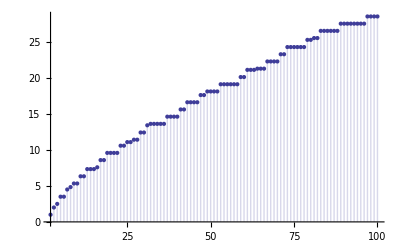

```mathematica
DiscretePlot[ FF[n,0], {n,2,100}]
```

```mathematica
FF2[ n_, k_ ] := Sum[ BernoulliB[k] / k! + N[MangoldtLambda[j]/Log[j]] FF2[n/j, k+1], {j,2,n}]
```

```mathematica
DiscretePlot[ FF2[n,0], {n,2,100}]
```

-Graphics-

```mathematica
(Floor[n]-1)BernoulliB[0] / 0!
```

-1+Floor[n]

```mathematica
FF3[n_, k_] := (n-1)/k - Sum[ FF3[n/j, k+1],{j,2,n}]
```

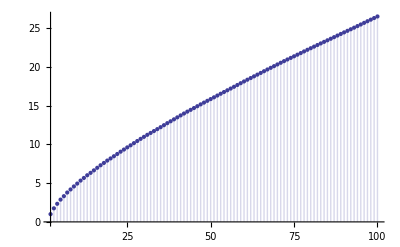

```mathematica
DiscretePlot[ FF3[n,1], {n,2,100}]
```

```mathematica
a[n_]:=-(n-1)!^(-1)*Sum[BernoulliB[j]/j*StirlingS1[(n-1),j-1]*(-1)^(n-1) ,{j,1,(n-1)+1}];
a[0] = -1;
a[-1]=1;Table[N[a[n]],{n,-1,19}]
```

{1.,-1.,0.5,0.0833333,0.0416667,0.0263889,0.01875,0.0142692,0.0113674,0.00935654,0.00789255,0.00678585,0.00592406,0.00523669,0.0046775,0.00421495,0.0038269,0.00349735,0.0032145,0.00296945,0.00275539}

```mathematica
FF4[ n_, k_ ] := Sum[ -a[k]N[MangoldtLambda[j]/Log[j]] -FF4[n/j, k+1], {j,2,n}]
```

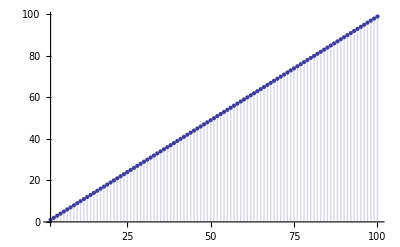

```mathematica
DiscretePlot[ FF4[n,0], {n,2,100}]
```

```mathematica
FF4[83,0]
```

82.

```mathematica
FF5[ n_, k_ ] := Sum[-a[k]N[MangoldtLambda[j]/Log[j]] - MoebiusMu[j] FF5[n/j, k+1], {j,2,n}]
```

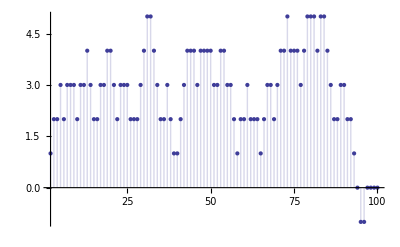

```mathematica
DiscretePlot[ FF5[n,0], {n,2,100}]
```